```mathematica
(*Chart from a particular sensor*)
Databins[][[2]]["Data"]
```

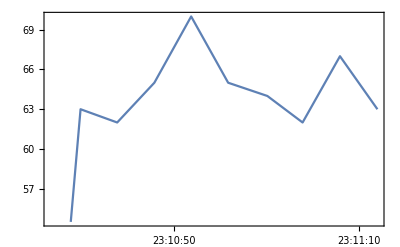

```mathematica
DateListPlot[Databins[][[2]]["Data"]["Gas1"]]
```

```mathematica
Databins[][[2]]["Data"]["Gas1"]["Values"]
```

{37.,63.,62.,65.,70.,65.,64.,62.,67.,63.}

```mathematica
Table["Gas"<>ToString[i],{i,10}]
```

{Gas1,Gas2,Gas3,Gas4,Gas5,Gas6,Gas7,Gas8,Gas9,Gas10}

```mathematica
Map[Last[Databins[][[2]]["Data"][#]["Values"]]&,Table["Gas"<>ToString[i],{i,10}]]]
```

```mathematica
Legended[ListLinePlot[{63.,61.,50.,56.,50.,39.,32.,32.,33.,33.},ColorFunction ->"NeonColors"],BarLegend["NeonColors"]]
```

-Graphics-

```mathematica
ServiceExecute["Twitter"]
```

```mathematica
RunScheduledTask[SendMessage["Twitter",Legended[ListLinePlot[{63.,61.,50.,56.,50.,39.,32.,32.,33.,33.},ColorFunction ->"NeonColors"],BarLegend["NeonColors"]]],1800]
```

```mathematica
sensors={GeoPosition[{41.383,2.10587}],GeoPosition[{41.3846,2.11191}],GeoPosition[{41.3859,2.11708}],GeoPosition[{41.3866,2.11993}],GeoPosition[{41.3872,2.12252}],GeoPosition[{41.3888,2.12873}],GeoPosition[{41.3905,2.13537}],GeoPosition[{41.3913,2.13864}],GeoPosition[{41.3925,2.14373}]};
GeoGraphics[{PointSize[.03],Map[{ColorData["NeonColors"][#[[1]]/90.],Point[#[[2]]]}&,Transpose[{values,sensors}]]}]
```